### Start choosing the example:

```mathematica
t=19;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{4,I2}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
(rule = CriticalCongestionSolver2[d2e = D2E[Data/.{I1->10,I2->1,U1->0,S1->0,S2->0,S3->0,S4->0,S5->0,S6->0}]];)//Timing
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

{u11==12&&u10==21&&u1==21,u1==u10,u1==9+u11}

True

{True,True}

True

{True}

True

Finished with the us!

Done!

{0.131487,Null}

```mathematica
(rule = CriticalCongestionSolver2[d2e ];)//Timing
```

EliminateVarsSimplify for the us

{u11==12&&u10==21&&u1==21,u1==u10,u1==9+u11}

True

{True,True}

True

{True}

True

Finished with the us!

Done!

{0.018458,Null}

```mathematica
d2e["uvars"]/.rule
```

<|{1,1->2}→21,{2,1->2}→11,{2,2->3}→11,{3,2->3}→0,{2,2->4}→11,{4,2->4}→12,{3,3->ex3}→0,{ex3,3->ex3}→0,{en1,en1->1}→21,{1,en1->1}→21,{en4,en4->4}→12,{4,en4->4}→12|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->0,I2->0(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->0,S2->1,S3->0,S4->0,S5->0,S6->0}];//Timing
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[jt397]&&NonNegative[1-jt397]&&NonNegative[1-jt397]&&NonNegative[-1+jt397]&&NonNegative[-1+jt397]&&NonNegative[1-jt397]&&NonNegative[2-u407]&&NonNegative[2-u407+u409]&&NonNegative[-2+u407]&&NonNegative[-1+u409]&&NonNegative[-1+u407-u409]&&NonNegative[1-u409]&&NonNegative[u409-u412]&&(jt397==0||1-jt397==0)&&(1-jt397==0||-1+jt397==0)&&(-1+jt397==0||1-jt397==0)&&(jt397==0||2-u407==0)&&(1-jt397==0||2-u407+u409==0)&&(1-jt397==0||-2+u407==0)&&(-1+jt397==0||-1+u409==0)&&(-1+jt397==0||-1+u407-u409==0)&&(1-jt397==0||1-u409==0)
and the rules are:
<|j387→1,j388→0,u416→0,j383→1,j384→1,j385→0,j386→1,j389→0,j390→0,j391→0,j392→0,j393→0,j394→0,jt395→0,jt396→1,jt398→1-jt397,jt399→1-jt397,jt400→-1+jt397,jt401→-1+jt397,jt402→1-jt397,jt403→1,jt404→0,jt405→0,jt406→0,u410→0,u413→-1+u407,u414→-1+1,u415→u409,u417→u407,u418→u412,u408→1,u411→u407|>

DataToEquations: The system is:
jt397==1&&u407==2&&u409==1&&u409≥u412
and the rules are:
<|j387→1,j388→0,u416→0,j383→1,j384→1,j385→0,j386→1,j389→0,j390→0,j391→0,j392→0,j393→0,j394→0,jt395→0,jt396→1,jt398→1-jt397,jt399→1-jt397,jt400→-1+jt397,jt401→-1+jt397,jt402→1-jt397,jt403→1,jt404→0,jt405→0,jt406→0,u410→0,u413→-1+u407,u414→-1+1,u415→u409,u417→u407,u418→u412,u408→1,u411→u407|>

DataToEquations: It took 0.010038 seconds to reduce with NewReduce!

DataToEquations: Possible multiple solutions 
{u412≤1,<|j387→1,j388→0,u416→0,j383→1,j384→1,j385→0,j386→1,j389→0,j390→0,j391→0,j392→0,j393→0,j394→0,jt395→0,jt396→1,jt398→1-1,jt399→1-1,jt400→-1+1,jt401→-1+1,jt402→1-1,jt403→1,jt404→0,jt405→0,jt406→0,u410→0,u413→-1+2,u414→-1+1,u415→1,u417→2,u418→u412,u408→1,u411→2,jt397→1,u407→2,u409→1|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{0.029979,Null}

<|{1,1->2}→2,{1,en380->1}→2,{2,1->2}→1,{2,2->3}→1,{2,2->4}→1,{3,2->3}→0,{3,3->ex382}→0,{4,2->4}→1,{4,en381->4}→u412,{en380,en380->1}→2,{en381,en381->4}→u412,{ex382,3->ex382}→0|>

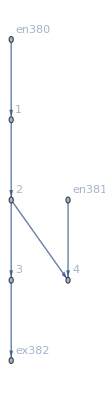

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]](*//KeySort*)
```

<|j387→1,j388→0,u416→0,j383→1,j384→1,j385→0,j386→1,j389→0,j390→0,j391→0,j392→0,j393→0,j394→0,jt395→0,jt396→1,jt398→0,jt399→0,jt400→0,jt401→0,jt402→0,jt403→1,jt404→0,jt405→0,jt406→0,u410→0,u413→1,u414→0,u415→1,u417→2,u418→u412,u408→1,u411→2,jt397→1,u407→2,u409→1|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j383→1,j384→1,j385→0,j386→1,j387→1,j388→0,j389→0,j390→0,j391→0,j392→0,j393→0,j394→0,jt395→0,jt396→1,jt397→1,jt398→0,jt399→0,jt400→0,jt401→0,jt402→0,jt403→1,jt404→0,jt405→0,jt406→0,u407→1.41151,u408→0.705756,u409→0.705756,u410→0,u411→1.41151,u413→0.705756,u414→0,u415→0.705756,u416→0,u417→1.41151,u418→u412|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```